# Unit 1 - Getting Started with Mathematica

This unit covers the following topics.

Basic introduction

Some tricks, good and bad

Assigning values to variables

Adding comments

More about palettes

Symbolic computing

## Basic introduction

First of all, Mathematica is a calculator which everyone can use without reading its “user’s manual”. Type a Mathematica command, then, hold down the key ⇧ and press the key ⌤ to execute the command. For example, type 1+2, press ⌤ while holding down ⇧, and Mathematica outputs 3 as the result of the evaluation.

```mathematica
1+2
```

3

It is that simple. Please play with Mathematica for a while.

Mathematica is a very powerful computing tool. Its commands can be so simple, as shown in the example, that it seems no study is needed. But they can also be so complicated and look so strange at first that it takes many days and weeks for new users to get used to the system. This section as well as this unit is to give you some basic and important introduction about using Mathematica.

You may also execute the command in a cell by right-clicking the cell and choosing Evaluate Cell on the pop-up menu.

It is unnecessary to move the cursor to the end of the command in a cell to execute the command. The cursor can be at any position in the cell.

Two basic concepts, a Mathematica session and the Mathematica workspace
A Mathematica session is the time period of running Mathematica from starting the software to terminating it.

The Mathematica workspace refers to the status of a Mathematica session, consisting of the variables you have created and their present values assigned as well as the functions you have defined during the session. It also contains built-in variables and their present values, such as % that refers to the most recent computing result.

Front end of Mathematica

-Graphics-

In this screenshot of Mathematica 10 are two Mathematica notebooks. A Mathematica notebook is a document in which you edit text, and input and execute Mathematica code. A notebook is saved as a .nb file by default. It can also be saved to document in different formats, including PDF document. But if you want to reopen the file in Mathematica, it must be saved as .nb document.

A Mathematica notebook consists of one or more cells. Cells are exactly like paragraphs in an article which help make the article well organized and more readable. A cell is also a container which contains text, Mathematica code (input), Mathematica output, and even cells.

In a Mathematica session, you can open and work on multiple notebooks. Different notebooks share one single workspace, which means a variable or function defined in one notebook can be accessed in another notebook. Notebooks even share the numbering of input and output.

Use keyboard or palettes?

We can type Mathematica commands in two ways.

The first method is to format input through palettes and/or short-cuts like Ctrl-2, Ctrl-^, Ctrl-_, and Ctrl-/. What is a palette? It is a graphical control panel with buttons which help users type Mathematica commands. You may start the menu item Palettes → Basic Math Assistant and explore tabs like Basic, Advanced, Basic Commands, and Typesetting, and use the palette to type, say, √(x^2-3x+1), ∑_(i=1)^100 (2i+1), and f(x)=Piecewise[{{2x-1,, x<0}, {x^2 ⅇ^-x,, x≥0}}].

It is really cool, isn’t it? Indeed, they do provide great convenience for us to type some typical and complicated commands. The input looks also professional.

But, if we use palettes, we will have to leave the keyboard and turn to mouse, touch screen or so. Moreover, because Mathematica uses invisible information to control the display of your input, editing your input might usually cause trouble you can never understand due to the fact that some invisible information may be deleted.

The second method is to type commands linearly on the keyboard without using any above-mentioned short-cut. The common arithmetic operators are +,-,* (multiplication), /, and ^ (such as 10^5 for 10^5).

You are strongly encouraged to take the second approach unless you use it as a word processor at the same time or type Greek letters and special symbols, such as α, β, ∞,∈,Δ, etc. If you just want to use the keyword, you still can type this group of letters by typing  Esc key, name of the letter, and Esc key. For example,

EscalphaEsc for α                           EscinfEsc  for ∞
EscceEsc    for ε                           EscpiEsc   for π
EscdEsc     for δ                           Esc!=Esc   for ≠
EscDEsc     for Δ                           Esc~~Esc   for ≈
EsceeEsc    for ⅇ (natural base)            EscelemEsc for ∈
EsccrossEsc   for × (cross product)

How to type ≤,≥, and → on the keyboard?

In Mathematica Input mode, type <= and any one more key to get ≤. Similarly, type >= (or ->) plus one more key to get ≥ (or →).

Give me a numerical result

```mathematica
1+2*(3-4)/5
```

3/5

```mathematica
1+2×(3-4)/5
```

3/5

By default, Mathematica always seeks an exact solution if possible, which is great in many cases. But, in many other cases, this may produce an awkward output presented on multiple lines and even pages, and a simple numerical result is certainly better. Besides, we feel often comfortable with a (numerical) number instead of a fractional number.

There are different ways to obtain a numerical result. The common ways are 1) Adding a decimal point to any number in a mathematical expression, or 2) Applying the built-in function N to the output.

```mathematica
1+2*(3.-4)/5
```

0.6

```mathematica
1+2×(3-4)/5//N
```

0.6

```mathematica
N[1+2*(3-4)/5]
```

0.6

```mathematica
Solve[2x^3-3x+4==0,x]
```

{{x→-(4-√14)^(1/3)/2^(2/3)-1/(2 (4-√14))^(1/3)},{x→((1+ⅈ √3) (4-√14)^(1/3))/(2 2^(2/3))+(1-ⅈ √3)/(2 (2 (4-√14))^(1/3))},{x→((1-ⅈ √3) (4-√14)^(1/3))/(2 2^(2/3))+(1+ⅈ √3)/(2 (2 (4-√14))^(1/3))}}

```mathematica
Solve[2x^3-3x+4==0.,x] (* decimal point is added to 0 *)
```

{{x→-1.64743},{x→0.823713-0.731786 ⅈ},{x→0.823713+0.731786 ⅈ}}

```mathematica
Solve[2x^3-3x+4==0,x]//N
```

{{x→-1.64743},{x→0.823713-0.731786 ⅈ},{x→0.823713+0.731786 ⅈ}}

```mathematica
N[Solve[2x^3-3x+4==0,x]]
```

{{x→-1.64743},{x→0.823713-0.731786 ⅈ},{x→0.823713+0.731786 ⅈ}}

Which one to use, ( ), [ ], or { }?

Now that you have mastered how to use Mathematica as a simple calculator, to explore and use its full power, we must be able to tell the difference of the usage of parentheses, square brackets, and curly braces. Knowing the difference is the key to master Mathematica.

( )  Parentheses are applied to control the order of evaluation. Such as, in the expression 1+2*(3-4)/5, we want Mathematica to evaluate 3-4 first before other operations. The usage is exactly the way we see in mathematics.

[ ] Square brackets are used when we call a function. For example, sin x will be Sin[x]. Similarly, sin(1+2*(3-4)/5) must be Sin[1+2*(3-4)/5]. How about sin^2 x? Can we type Sin^2[x]? No, because that means Sin^2 is a function! But there is no such a function. We input Sin[x]^2.

{ } Curly braces are used to create a list. Such as {1,2,3}. While a function asks for one single argument but we want to provide it with multiple items, we put all the items into a list and feed it to the function.

We are to see more examples now.

```mathematica
Sqrt[5]
```

√5

```mathematica
√5
```

√5

Why does Mathematica simply return exactly what I input? Again, it seeks to find an exact solution but cannot. We can force Mathematica to produce a numerical approximation by adding a decimal point to a number in the expression to be evaluated or applying the built-in function N to the expression.

```mathematica
Sqrt[5.]
```

2.23607

```mathematica
√5//N (* the same as N[√5] *)
```

2.23607

For other cases, you obtain exactly what you input instead of what you expect because, usually, you have misspelled a built-in function or accessed a variable which is not defined, i.e., no value has been assigned to it.

If there are blue colored symbols in the input, they are either misspelled or undefined.

```mathematica
Sin[x]  (* the variable x is undefined *)
```

Sin[x]

```mathematica
sin[3.14] (* the symbol sin is undefined *)
```

sin[3.14]

Let’s remember that the square brackets [ ] are reserved for calling a function. When calling a function, we must use [ ] right after the name of the function. The rule is that simple. However, because we get used to the notation like sin(x) for years, many tend to make a common mistake related to this rule.

```mathematica
Sin(Pi/2) (* incorrect input *)
```

(π Sin)/2

```mathematica
Sin{Pi/2} (* incorrect input *)
```

{(π Sin)/2}

```mathematica
Sin Pi/2 (* incorrect input *)
```

(π Sin)/2

The correct input is using square brackets [ ] right after the name of a function.

```mathematica
Sin[Pi/2]
```

1

```mathematica
Sin^2[Pi/3] (* incorrect input for sin^2 π/3. is sin^2 a function? *)
```

Sin^(2[π/3])

```mathematica
(Sin^2)[π/3]
```

Sin^2[π/3]

```mathematica
Sin[Pi/3]^2 (* correct input for sin^2 π/3*)
```

3/4

Never use square brackets [ ] and curly braces { } to control the order of computation in an algebraic expression as we do manually in algebra. Use only parentheses ( ) for the purpose.

```mathematica
2{2-5 [6-4(2+3 5)]} (* incorrect usge of [ ] and { } *)
```

{2 (2-5[-62])}

```mathematica
2(2-5 (6-4(2+3 5)))
```

624

Now, we are to see how to use { }. It is used to create an object called a list. For example, 1, 2, 3, 4, and 5 are five individual objects, but the list {1, 2, 3, 4, 5} is just one object with five elements. We can put various types of objects into a list. For example, {{-1,0,1},{-2,0,1,2}}, {Sin, π, 1, 2}, and {{i, 10}, 1, 100, 2} are each a list.

Lists are a powerful mechanism of Mathematica. If using them properly, we can use less code to do more things efficiently. We will study how to construct and manipulate lists in detail in Unit 3.

In some cases, we have to use a list. For example, the built-in function Plot draws the graph of a single-variable function f(x) in Cartesian coordinate system. The basic usage is shown below.

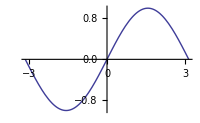

```mathematica
Plot[Sin[x],{x,-Pi,Pi},ImageSize->200]
```

But how to plot the graphs of multiple functions on one figure? We will have to put all these functions into a list as follows.

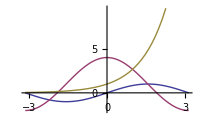

```mathematica
Plot[{Sin[x],3Cos[x]+1,E^x},{x,-Pi,Pi},ImageSize->200] (* PlotLegend->{Sin[x],3Cos[x]+1,E^x} *)
```

Similarly, the built-in functions Solve and NSolve are each used to solve an equation. To solve a system of equations, we need to place all the equations in a list.

```mathematica
Clear[x] (* remove x from Mathematica workspace to guarantee that x is a symbol without a value assigned to it *)
Solve[2x^3-3x+4==0.,x]
```

{{x→-1.64743},{x→0.823713-0.731786 ⅈ},{x→0.823713+0.731786 ⅈ}}

```mathematica
Clear[x,y]
NSolve[{2x+3y==0,x-y==5},{x,y}]
```

{{x→3.,y→-2.}}

All built-in functions and names of a constant, an option of a function or value of an option, such as Sin, Cos, Log, Tan, E (natural base, about 2.71828), Pi, Filling, Green, etc., each start with a capital letter. If a built-in name contains multiple English “words”, then, each word must start with a capital letter, such as ArcSin, PlotRange, FillingStyle, and so on.

Some basic mathematical functions
Abs
Sqrt, the name for √x
Sin, Cos, Tan, Cot,
ArcSin, ArcCos, ArcTan, ArcCot
Exp, the name for E^x
Log, the name for natural logarithm; there is no Ln
Log10, the name for common logarithm log_10 x
n ! or Factorial

Suppressing output of a command

If an assignment statement is followed by the semicolon “;”, no output is displayed. Usually, after debugging our code, we had better add semicolons to most assignment statements so as to keep our output clear and clean.

```mathematica
x=5
y=6;
z=7;
```

5

Wolfram Documentation (or Documentation Center)

Wolfram Documentation is an off-line help system built in Mathematica. It provides various types of resources users may need. We can access it through the menu item, Help → Wolfram Documentation.

In many cases, we have to explore the Wolfram Documentation for information about the usage of built-in functions. For a built-in function, there may be a number of examples. It is always an efficient way to study and follow good examples.

To find information on a built-in function or symbol, you can visit the Wolfram Documentation and search for the name of the function or symbol. You may move the cursor to the name and press F1 key.

## Some tricks, good and bad

The symbol % is reserved to referring the most recent result of calculation, and space between two symbols or between a symbol and a number stands for multiplication. They seem very good and kind. But both tend to be trouble makers.

```mathematica
1+2*(3-4)/5
```

3/5

```mathematica
N[%]
```

0.6

```mathematica
x=2;
y=3;
```

Variables x and y are assigned the values of 2 and 3, respectively.

```mathematica
x*y
```

6

```mathematica
x y
```

6

```mathematica
5x
```

10

```mathematica
xy
```

xy

Can you discover what is wrong in the last command? Yes, there is no SPACE between variables x and y and, thus, xy is a variable to which no value has been assigned. This is possibly the most frequently seen trivial mistake. Therefore, to save your time, DO NOT use this silly way for multiplication. I heard some professors complain about it, wishing it be removed from Mathematica eventually.

Then, how about %? Don’t depend on it. When moving the cursor from one cell to another in a Mathematica notebook, you might be easily misled and troubled by the value % refers. Remember that it always refers to the most recent result of evaluation. With %, time order places a vital role, which may not be reflected exactly in your Mathematica notebook.

Mathematica even allows users to use %%, %%%, %%%%, etc. I believe you can guess what values they refer, i.e., the next, the second, the third, and so on, most recent results of evaluation. Forget about all these. If you need the very values, assign the values to your own variables.

## Assigning values to variables

The name (or identifier) of a variable, function, or constant consists of human language letters (including English letters, Chinese characters, etc.), digits, and/or $ (dollar sign). It must start with a human language letter or $, such as, x, y, x1, $0x, student1, Student$01a. By the way, it is not recommended to use $. If you use, use it consistently for dedicated purpose. For example, in a large project involving hundreds and thousands of lines of Mathematica code, you may use names beginning with $ to control the communication between functions and/or Modules/Blocks (see Unites 4 and 6). But the fewer of this kind of variables, the easier it is for you to maintain and manage your code.

The symbol = (Set) assigns a value or the evaluated result of an expression to a variable.

The symbol := (SetDelayed) assigns a value or an unevaluated expression to a variable. It is a delayed assignment.

The symbol == (double equal signs) is used to determine if two values are equal.

```mathematica
x=RandomInteger[{0,100}]
```

93

The variable x has been assigned a value. It will not change until it is assigned a new value.

```mathematica
x
```

93

```mathematica
x
```

93

```mathematica
x:=RandomInteger[{0,100}]
```

The variable x has not been assigned a concrete value. It has recorded what to do when it is accessed.

```mathematica
x (* RandomInteger is called to generate a random integer number in the range from 0 to 100. *)
```

85

```mathematica
x (* RandomInteger is called again to generate a new random integer number. *)
```

48

Now, you should understand the following two groups of commands and their output.

```mathematica
x=RandomInteger[{0,100}]; {x,x,x,x,x}
```

{2,2,2,2,2}

```mathematica
x:=RandomInteger[{0,100}]; {x,x,x,x,x}
```

{91,70,3,81,57}

## Adding comments

It is always a good practice to add comments to your code. With Mathematica, you can click the ⊕ icon and then click the menu item, Plain text, to start a new cell. In the new cell, you can type whatever you want. When you evaluate the present notebook by choosing menu item Evaluation → Evaluate Notebook or pressing first Ctrl-A and then ⇧-⌤, Mathematica executes all commands with contents in the plain text cells skipped.

How to bring the ⊕ icon up if it doesn’t show? When you are at the end of a notebook, click at any point after the last cell you have input; when you are in the middle of a notebook, click any point in between two cells.

-Graphics-

However, if you want to add comments into your Mathematica code, you can do so by quoting comments in between (* and *) and placing it anywhere you think proper.

```mathematica
x:=Random[](* this is a delayed assignment *)
x (* this gives the first random number *)
x (* This gives the second random number. The two numbers are usually different. *)
```

0.95491

0.9374

## More about palettes

As mentioned at the beginning of this unit, palettes enable users to prepare mathematical expressions in professional format. But users are strongly encouraged to type on the keyboard without even using short-cut like Ctrl-2, Ctrl-^, and Ctrl-_.

Through Palettes → Basic Math Assistant → Advanced, we can type the following commands easily.

```mathematica
5.^(1/3)
```

1.70998

```mathematica
∑_(i=1)^100 i (* 1+2+3+⋯+100 *)
```

5050

```mathematica
Clear[x] 
∫_0^π Sin[x]ⅆx
```

2

But there is always a Mathematica name for every command that can be typed via palettes, such as Sum for ∑_(index=start)^end expr and Integrate for ∫exprⅆvar. In most cases, names are preferred.

The Mathematica names give us flexibility and even extra options to control the behavior of a function. For example, Sum can take any step, while ∑_(index=start)^end expr has a predetermined step, i.e., 1; and Integrate can be used to find both indefinite and definite integrals. In addition, we often have to go back and edit commands. When we use palettes to input, say, ∑_(index=start)^end expr, we may delete by accident a box like the one for “end”. If this happens, we may not be able to restore the box and, thus, have to type the whole command again. But this is never a problem when we input by using Mathematica names. More importantly, palettes like ∑_(index=start)^end expr are actually like 2-D graphs. To display the palettes properly, Mathematica has to use various information to guide and control the display. Except the developers of Mathematica, users don’t know even the existence of such information. We have seen often in computer labs that formulas, prepared by some students via palettes, look perfect but never work. The problem is usually caused by accidental removal of this kind of hidden information when they edit the formulas. Our suggestion is always either to delete the formulas and retype them or to use Mathematica names such as Sum.

```mathematica
5.^(1/3)
```

1.70998

```mathematica
Sum[i,{i,1,100}] (* 1+2+3+⋯+100 *)
```

5050

```mathematica
Sum[i,{i,1,100,2}] (* 1+3+5+⋯+99 *)
```

2500

```mathematica
Sum[i,{i,50,100,3}] (* 50+53+56+⋯+98 *)
```

1258

```mathematica
Integrate[Sin[x],x]
```

-Cos[x]

```mathematica
Integrate[Sin[x],{x,0,Pi}]
```

2

## Symbolic computing

Mathematica is a computer algebra system (CAS), a software system that can not only solve problems numerically but also do symbolic operations. The most frequently used built-in function for symbolic and algebraic computation is possibly Simplify, especially when we exam our result from evaluating an indefinite integral or a “complicated” algebraic expression. The other commonly used functions include at least Factor, Expand, Apart, and Together.

Certainly, D and Integrate are two very frequently used symbolic computing functions for calculus students. They are discussed in Units 5 and 9.

Simplify

It performs algebraic and other operations on the input and returns the simplest form it can find. Since Mathematica does not simplify the output of other built-in functions, Simplify is possibly the most frequently applied function when we do symbolic computing.

```mathematica
3x(1+x)+2x^2+1
```

1+2 x^2+3 x (1+x)

It turns out that Mathematica does nothing except rearranging the order of the input polynomial. In this case, Simplify can force Mathematica to combine like terms.

```mathematica
Simplify[3x(1+x)+2x^2+1]
```

1+3 x+5 x^2

```mathematica
Integrate[E^-x Cos[2x],x]
```

-1/5 ⅇ^-x (Cos[2 x]-2 Sin[2 x])

```mathematica
D[%,x](* differentiation. it doesn't give E^-x Cos[2x] as expected *)
```

-1/5 ⅇ^-x (-4 Cos[2 x]-2 Sin[2 x])+1/5 ⅇ^-x (Cos[2 x]-2 Sin[2 x])

```mathematica
Simplify[%] (* now, it works *)
```

ⅇ^-x Cos[2 x]

Factor

It factors a polynomial.

```mathematica
Factor[x^2+3x-10]
```

(-2+x) (5+x)

```mathematica
Factor[x^2+3.1 x-0.32]
```

(-0.1+1. x) (3.2+1. x)

Expand

It does the opposite operation of Factor.

```mathematica
Expand[(x-2)(x+5)]
```

-10+3 x+x^2

```mathematica
%//TraditionalForm
```

x^2+3 x-10

Apart

Calculus II covers the method of partial fractions, which decomposes a rational expression into partial fractions, in the chapter on integration techniques. Solving differential equations may also require the skill. Apart is for the job.

```mathematica
Apart[ (5x+6)/(x^2+3x-10)]
```

16/(7 (-2+x))+19/(7 (5+x))

Together

It is the opposite operation of Apart. It combines multiple rational expressions into a single rational function.

```mathematica
Together[16/(7 (-2+x))+19/(7 (5+x))]
```

(6+5 x)/((-2+x) (5+x))

## Lab 1

Compute both exact and numerical value for each of the following expressions.

(10^2-4(11-5)^3)/(5^6-6^5)

ln 25^3/7^2

log (133/5)

Apply Simplify to each of the following expressions.

ln (8/E^3)

1/2(1-cos 2x)

cos^2 2x+sin^2 2x

Factor each polynomial.

2 x^6+6 x^5-36 x^4-56 x^3+240 x^2-256

3 x^3+21 x^2-15x-225

x^2-5x-24

Apply Apart to each rational function.

(x^3+3 x^2-5x+1)/(3 x^3+9 x^2-12)

(x^4-5x+1)/(3 x^3+9 x^2-12)

(3 x^2-5x+1)/(3 x^3+9 x^2-12)

Find and study basic examples for Plot in the Wolfram Documentation. Then, plot the graph of f(x)=x^2-5x-24 on the interval [-1,6].

Plot on one figure the graphs of f(x)=x^2-5x-24,g(x)=5sin x-24, and h(x)=5cos x-24 on the interval [-1,6].

Do experiment with the following two groups of commands, recognize and explain the difference in their outputs.

x = RandomInteger[{1,25} ];  {x, x, x}

x := RandomInteger[{1,25} ]; {x, x, x}

Compute the following sums, and make a conjecture about the value of ∑_(i=1)^(10^n) i, where integer n≥1.

∑_(i=1)^10 i

∑_(i=1)^100 i

∑_(i=1)^1000 i

∑_(i=1)^10000 i

∑_(i=1)^100000 i

Somehow Mathematica occupies the whole computer screen, and you seem to have lost any control of your computer. Mathematica is possibly in Full Screen mode. To exit the mode, right click the mouse at any point on the screen, and click Toggle Full Screen at the bottom of the pop-up menu.

© 2015-2023 by David Wang, dwang@liberty.edu